```mathematica
ρ0=1;
L1=12;
L2=12;
γ=1.4;
c=1.4;
eps=0.001;
alphaa=2;
timeP = 4.0;
initrho[r_]:=eps Exp[-alphaa r^2]
```

```mathematica
NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]
```

NIntegrate::inumr: The integrand initrho[x,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4},{0,4}}.

NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]

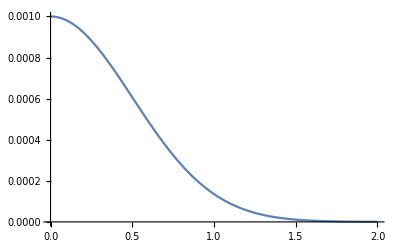

```mathematica
Plot[initrho[r],{r,0,2}]
```

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=eps/(2alphaa)NIntegrate[Exp[-ξ^2/(4alphaa)]Cos[ξ t]BesselJ[0,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
uAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(x-L1/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
vAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(y-L2/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
mcrCenterLine=MeshCellRcm[[nx ny/2+1;;nx ny/2+nx]];
```

```mathematica
mmm=Table[mcrCenterLine[[i]],{i,mcrCenterLine//Length}];
```

```mathematica
rhoAn[mmm[[1,1]],mmm[[1,2]],2.0]
```

2.45034×10^-17

#### Center values for graphics

```mathematica
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

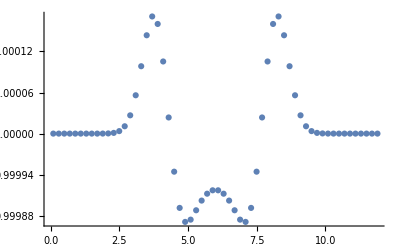

```mathematica
dataExact=ListPlot[dataAnCenterRhoEqP,PlotRange->All]
```

#### Mean integral values for error analysis

```mathematica
area=hx hy
```

0.04

```mathematica
centralCells=Table[{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]-hy/2,MeshCellRcm[[i,2]]+hy/2},{i,MeshCellRcm//Length}]
```

{{0.,0.2,0.,0.2},{0.2,0.4,0.,0.2},{0.4,0.6,0.,0.2},{0.6,0.8,0.,0.2},{0.8,1.,0.,0.2},{1.,1.2,0.,0.2},3588,{10.8,11.,11.8,12.},{11.,11.2,11.8,12.},{11.2,11.4,11.8,12.},{11.4,11.6,11.8,12.},{11.6,11.8,11.8,12.},{11.8,12.,11.8,12.}}
 |  |  |  |

Analytical values

```mathematica
fAn[t_,n_]:=eps/(2alphaa area)NIntegrate[Exp[-ξ^2/(4alphaa)]Cos[ξ t]BesselJ[0,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞},{x,centralCells[[n,1]],centralCells[[n,2]]},{y,centralCells[[n,3]],centralCells[[n,4]]},Method->{Automatic,"SymbolicProcessing"->False}]
```

```mathematica
meanInt=Table[fAn[timeP,i],{i,1,MeshCellRcm//Length}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.67611×10^-15 and 2.9983×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.71539×10^-15 and 1.46543×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.31694×10^-16 and 1.32213×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

Numerical values

```mathematica
meanNum=Table[(GetSol[alpha,i,1,{MeshCellRcm[[i,1]],(Lx+hx)/2}])-1,{i,1,MeshCellRcm//Length}]
```

{6.624×10^-8,5.22695×10^-7,2.49367×10^-6,8.47218×10^-6,0.0000220915,0.0000459602,0.0000778663,0.000108287,0.000122986,0.00011095,0.0000723613,0.00001981,-0.0000288103,-0.0000602348,-0.0000713103,-0.0000673667,-0.0000566071,-0.0000453522,-0.0000364869,-0.0000303574,-0.000026273,-0.0000234791,-0.0000214727,-0.0000199766,-0.0000188425,-0.0000179846,-0.0000173482,-0.0000168973,-0.0000166083,-0.0000164671,-0.0000164671,-0.0000166083,-0.0000168973,-0.0000173482,-0.0000179846,-0.0000188425,-0.0000199766,-0.0000214727,-0.0000234791,-0.000026273,-0.0000303574,-0.0000364869,-0.0000453522,-0.0000566071,-0.0000673667,-0.0000713103,-0.0000602348,-0.0000288103,0.00001981,0.0000723613,0.00011095,0.000122986,0.000108287,0.0000778663,0.0000459602,0.0000220915,8.47218×10^-6,2.49367×10^-6,5.22695×10^-7,6.624×10^-8}

```mathematica
Norm[meanInt-meanNum,∞]
Norm[meanInt-meanNum,1]
Norm[meanInt-meanNum,2]
```

4.58332×10^-6

0.0000559974

0.0000121205